62.8123 Ω

159.205 mA

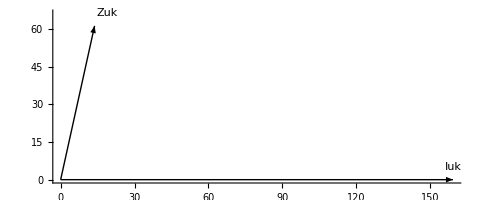

```mathematica
(* Ovdje se unose tražene veličine. Veličine morate pretvoriti na osnovne jedinice (npr. 99 mF = 99*10^(-3) F). Veličine upisujete bez jedinica.*)
R1 = 10; 
R2 = 4; 
f = 100; 
c = 97*10^(-6); 
L = 99*10^(-3); 
u= 10;
(* Ovdje je račun. Na kraju računa su dodane "varijable" Ω i mA kako bi u ispisu dobili jedinice na kraju ispisa.*)
ω = 2*Pi*f; 
XL = I*ω*L; 
XC = -I/(ω*c); 
Z = R1 + XL + (R2*XC)/(R2 + XC); 
ZUK = Abs[Z]*Ω//N
IUK = ((u*Ω)/ZUK)*1000mA
Graphics[{{Arrow[{{0, 0}, {IUK/mA, 0}}]}, 
   {Arrow[{{0, 0}, {Re[Z], Im[Z]}}]}, Text["Iuk", {IUK/mA, 5}], 
   Text["Zuk", {Re[Z] + 5, Im[Z] + 5}]}, Axes -> True]
```